## Model of the NF-κB signaling module

This is an exmaple of converting an xCellerator model into SBML format based on the NF-kappa-B model of Hoffman et. al.

Model Courtesy of Andre Levchenko, Jonhs Hopkins University

References: 
1. Hoffmann, A.,* Levchenko, A.,* Scott, M.L., Baltimore, D. THe IkappaB-NF-kappaB signaling module:temporal control and selective gene activation. Science, 298: 1241, 2002

## xCellerator implementation

Created: 11 August 2005 BES (Mac OSX/Mathematica 5.2)
Verified: 7 Aug 2008 (Linux/Ubuntu 8.04/Mathematica 6.0.3)

```mathematica
<<xlr8r.m
```

xlr8r 0.68 (5 Aug 2008) loaded 07 August 2008 at 09:32 GMT-06:60 using Mathematica 6.0 for Linux x86 (32-bit) (June 2, 2008) (Version 6., Release 3) (MathSBML 2.8.1 [18-July-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

```mathematica
<<xlr8r2SBML.m
```

xlr8r2SBML Version 0.2 alpha (02 July 2007) using Mathematica Version 6.0 for Linux x86 (32-bit) (June 2, 2008) loaded 07-Aug-2008 09:32:26 (GMT-06:60)

Generate the reactions for the NF-κB signaling module

```mathematica
circuit={{IkBa + NFkB⇄ IkBa⎵NFkB , a1, d1},{IKK⎵IkBa + NFkB⇄ IKK⎵IkBa⎵NFkB , a2, d2},{NFkB⇄NFkBn,tr1,tr2},{IkBa⎵NFkB->NFkB, deg1},{IkBan + NFkBn⇄ IkBan⎵NFkBn , a1, d1},{IKK+IkBa⇄IKK⎵IkBa,a3,d3},{IkBat->∅,deg3},{IkBa⇄IkBan,tr3,tr4},{IKK⎵IkBa⎵NFkB->IKK+NFkB,k1},{IKK⎵IkBa->IKK,k2},{IkBat↦IkBa,hill[vmax->0.8 3.06,khalf->10]},{IkBa⎵NFkB⇄IkBan⎵NFkBn,tr5,tr6},{IkBa->∅,deg2},{NFkBn↦IkBat,hill[vmax->0.83 1.2375,nhill->2,khalf->1]},{∅->IkBat,trb},{IKK+IkBa⎵NFkB⇄IKK⎵IkBa⎵NFkB , a4,d4},{IKK->∅,adapt}};
```

```mathematica
systemOfODEs=interpret[circuit];
```

Assign values to the rate constants

From reference (1)

```mathematica
systemConstants={
a1-> 30, a2-> 30, a3-> 1.35, a4-> 11.1,
tr1-> 5.4, tr2-> 0.0048, tr3-> 0.018, tr4-> 0.012,tr5-> 0, tr6-> 0.82944,
d1-> 0.03, d2-> 0.03, d3-> 0.0075, d4-> 0.105 ,
deg1-> 0.5 * 0.0027, deg2-> 0.5*0.0135, deg3-> 0.0168,
k1-> 1.221, k2-> 0.2442, trb-> 0.65*0.00014175, adapt-> 0.0072};
```

```mathematica
initialState={NFkB-> 0.003053, IkBa-> 0.372, IkBa⎵NFkB->0.09826,
NFkBn->.00047638,
IkBan->0.11937,
IkBan⎵NFkBn->0.001985,
IKK-> 0.1,
IkBat->0.008454217};
```

```mathematica
timeCourse=run[circuit,
initialConditions-> initialState,
rates-> systemConstants,
timeSpan-> 500];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {IKK⎵IkBa,IKK⎵IkBa⎵NFkB}

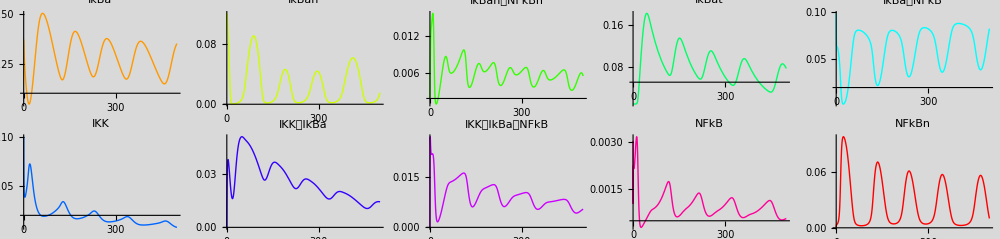

```mathematica
gridPlot[timeCourse, plotColumns-> 5, ImageSize-> 1000, Background-> LightGray]
```

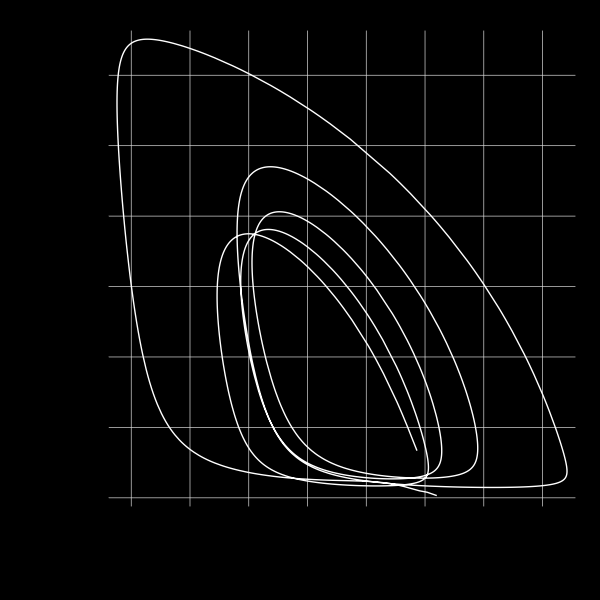

```mathematica
PhasePlot[timeCourse, {IkBa, NFkBn}, {0, 500},  ImageSize-> 600,FrameLabel-> {"IkBa", "NFkBn"}, Frame-> True, PlotStyle-> White, TextStyle-> {FontFamily-> Times, White, FontSize-> 18}, Background-> Black, AspectRatio-> 1, GridLines-> Automatic]
```

## Convert the xlr8r-model to SBML

```mathematica
<<xlr8r2SBML.m
```

xlr8r2SBML Version 0.2 alpha (02 July 2007) using Mathematica Version 6.0 for Linux x86 (32-bit) (June 2, 2008) reloaded 07-Aug-2008 09:37:11 (GMT-06:60)

```mathematica
circuit={{IkBa + NFkB⇄ IkBa⎵NFkB , a1, d1},{IKK⎵IkBa + NFkB⇄ IKK⎵IkBa⎵NFkB , a2, d2},{NFkB⇄NFkBn,tr1,tr2},{IkBa⎵NFkB->NFkB, deg1},{IkBan + NFkBn⇄ IkBan⎵NFkBn , a1, d1},{IKK+IkBa⇄IKK⎵IkBa,a3,d3},{IkBat->∅,deg3},{IkBa⇄IkBan,tr3,tr4},{IKK⎵IkBa⎵NFkB->IKK+NFkB,k1},{IKK⎵IkBa->IKK,k2},{IkBat↦IkBa,hill[vmax->0.8 3.06,khalf->10]},{IkBa⎵NFkB⇄IkBan⎵NFkBn,tr5,tr6},{IkBa->∅,deg2},{NFkBn↦IkBat,hill[vmax->0.83 1.2375,nhill->2,khalf->1]},{∅->IkBat,trb},{IKK+IkBa⎵NFkB⇄IKK⎵IkBa⎵NFkB , a4,d4},{IKK->∅,adapt}};
```

```mathematica
systemConstants={
a1-> 30, a2-> 30, a3-> 1.35, a4-> 11.1,
tr1-> 5.4, tr2-> 0.0048, tr3-> 0.018, tr4-> 0.012,tr5-> 0, tr6-> 0.82944,
d1-> 0.03, d2-> 0.03, d3-> 0.0075, d4-> 0.105 ,
deg1-> 0.5 * 0.0027, deg2-> 0.5*0.0135, deg3-> 0.0168,
k1-> 1.221, k2-> 0.2442, trb-> 0.65*0.00014175, adapt-> 0.0072};
```

```mathematica
initialState={NFkB-> 0.003053, IkBa-> 0.372, IkBa⎵NFkB->0.09826,
NFkBn->.00047638,
IkBan->0.11937,
IkBan⎵NFkBn->0.001985,
IKK-> 0.1,
IkBat->0.008454217};
```

```mathematica
sbml=convertToSBML[circuit, initialState, systemConstants, NFKappaBeta,NFKappaBeta, comp]
```

Warning: checkKineticLaw:  the species ⎵EmptySet is referenced in the reaction reaction12 = IkBat→⎵EmptySet but has not been previously defined.

<?xml version="1.0" encoding="UTF-8"?>
<!-- Generated 07-Aug-2008 09:37:28 (GMT-06:60) -->
<!-- Generated by MathSBML 2.8.1 [18-July-2008] -->
<!-- Generated using Mathematica Version 6.0 for Linux x86 (32-bit) (June 2, 2008) -->
<sbml xmlns="http://www.sbml.org/sbml/level2/version3"
    level="2"
    version="3">
 <annotation>
  <mathsbml:AuthorConfiguration xmlns:mathsbml="http://sbml.org/software/mathsbml/ns">
   <mathsbml:date>2008-08-07T09:37:27</mathsbml:date>
   <mathsbml:MachineDomain>gateway.2wire.net</mathsbml:MachineDomain>
   <mathsbml:MachineID>7100-91543-91800</mathsbml:MachineID>
   <mathsbml:MachineName>mathmans-linux-desktop</mathsbml:MachineName>
   <mathsbml:MachineType>PC</mathsbml:MachineType>
   <mathsbml:MathematicaVersion>6.0 for Linux x86 (32-bit) (June 2, 2008)</mathsbml:MathematicaVersion>
   <mathsbml:OperatingSystem>Unix</mathsbml:OperatingSystem>
   <mathsbml:ProcessorType>x86</mathsbml:ProcessorType>
   <mathsbml:ProductInformation mathsbml:ProductIDName="Mathematica"
       mathsbml:ProductKernelName="Mathematica 6 Kernel"
       mathsbml:ProductVersion="6.0 for Linux x86 (32-bit) (June 2, 2008)"
       mathsbml:ProductVersionNumber="6." />
   <mathsbml:SoftwareVersion>2.8.1 [18-July-2008]</mathsbml:SoftwareVersion>
   <mathsbml:System>Linux</mathsbml:System>
   <mathsbml:UserName>mathman</mathsbml:UserName>
  </mathsbml:AuthorConfiguration>
 </annotation>
 <model id="NFKappaBeta"
     name="NFKappaBeta"
     metaid="_NFKappaBeta">
  <notes>
   <body xmlns="http://www.w3.org/1999/xhtml">This model was auto-generated from xlr8r reactions by xlr8r2SBML version 0.2 alpha (02 July 2007) at 07-Aug-2008 09:37:26 (GMT-06:60)<p style="font-size:x-small;">This is a Systems Biology Markup Language (SBML) file, generated by MathSBML 2.8.1 [18-July-2008] 07-Aug-2008 09:37:27 (GMT-06:60). SBML is a form of XML, and most XML files will not display properly in an internet browser. To view the contents of an XML file use the &quot;Page Source&quot; or equivalent button on you browser.</p></body>
  </notes>
  <annotation>
   <rdf:RDF xmlns:rdf="http://www.w3.org/1999/02/22-rdf-syntax-ns#"
       xmlns:dc="http://purl.org/dc/elements/1.1/"
       xmlns:dcterms="http://purl.org/dc/terms/"
       xmlns:vCard="http://www.w3.org/2001/vcard-rdf/3.0#">
    <rdf:Description rdf:about="_NFKappaBeta">
     <dc:creator rdf:ParseType="Resource">
      <rdf:Bag>
       <rdf:li rdf:parseType="Resource">
        <vCard:N rdf:parseType="Resource">
         <vCard:Family>mathmans-linux-desktop at gateway.2wire.net (automatically generated)</vCard:Family>
         <vCard:Given>mathman (automatically generated)</vCard:Given>
        </vCard:N>
        <vCard:EMAIL>anonymous@gateway.2wire.net</vCard:EMAIL>
        <vCard:ORG>
         <vCard:Orgname>MathSBML User Community</vCard:Orgname>
        </vCard:ORG>
       </rdf:li>
      </rdf:Bag>
     </dc:creator>
     <dcterms:created rdf:parseType="Resource">
      <dcterms:W3CDTF>2008-08-07T09:37:27</dcterms:W3CDTF>
     </dcterms:created>
    </rdf:Description>
   </rdf:RDF>
  </annotation>
  <!-- <listOfFunctionDefinitions /> -->
  <!-- <listOfUnitDefinitions /> -->
  <!-- <listOfCompartmentTypes /> -->
  <!-- <listOfSpeciesTypes /> -->
  <listOfCompartments>
   <compartment id="comp"
       name="comp"
       spatialDimensions="3"
       units="volume"
       size="1." />
  </listOfCompartments>
  <listOfSpecies>
   <species id="NFkB"
       name="NFkB"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.003053"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IkBa"
       name="IkBa"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.372"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IkBa_NFkB"
       name="IkBa_NFkB"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.09826"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="NFkBn"
       name="NFkBn"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.00047638"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IkBan"
       name="IkBan"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.11937"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IkBan_NFkBn"
       name="IkBan_NFkBn"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.001985"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IKK"
       name="IKK"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.1"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IkBat"
       name="IkBat"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0.008454217"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IKK_IkBa"
       name="IKK_IkBa"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="IKK_IkBa_NFkB"
       name="IKK_IkBa_NFkB"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       initialConcentration="0"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
   <species id="_EmptySet"
       name="_EmptySet"
       compartment="comp"
       boundaryCondition="false"
       constant="false"
       substanceUnits="substance"
       hasOnlySubstanceUnits="false" />
  </listOfSpecies>
  <listOfParameters>
   <parameter id="a1"
       name="a1"
       value="30." />
   <parameter id="a2"
       name="a2"
       value="30." />
   <parameter id="a3"
       name="a3"
       value="1.35" />
   <parameter id="a4"
       name="a4"
       value="11.1" />
   <parameter id="tr1"
       name="tr1"
       value="5.4" />
   <parameter id="tr2"
       name="tr2"
       value="0.0048" />
   <parameter id="tr3"
       name="tr3"
       value="0.018" />
   <parameter id="tr4"
       name="tr4"
       value="0.012" />
   <parameter id="tr5"
       name="tr5"
       value="0" />
   <parameter id="tr6"
       name="tr6"
       value="0.82944" />
   <parameter id="d1"
       name="d1"
       value="0.03" />
   <parameter id="d2"
       name="d2"
       value="0.03" />
   <parameter id="d3"
       name="d3"
       value="0.0075" />
   <parameter id="d4"
       name="d4"
       value="0.105" />
   <parameter id="deg1"
       name="deg1"
       value="0.00135" />
   <parameter id="deg2"
       name="deg2"
       value="0.00675" />
   <parameter id="deg3"
       name="deg3"
       value="0.0168" />
   <parameter id="k1"
       name="k1"
       value="1.221" />
   <parameter id="k2"
       name="k2"
       value="0.2442" />
   <parameter id="trb"
       name="trb"
       value="0.00009213750000000001" />
   <parameter id="adapt"
       name="adapt"
       value="0.0072" />
  </listOfParameters>
  <!-- <listOfInitialAssignments /> -->
  <!-- <listOfRules /> -->
  <!-- <listOfConstraints /> -->
  <listOfReactions>
   <reaction id="reaction1"
       name="reaction1"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa" />
     <speciesReference species="NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa_NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>a1</ci>
       <ci>IkBa</ci>
       <ci>NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction2"
       name="reaction2"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa" />
     <speciesReference species="NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>d1</ci>
       <ci>IkBa_NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction3"
       name="reaction3"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa" />
     <speciesReference species="NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK_IkBa_NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>a2</ci>
       <ci>IKK_IkBa</ci>
       <ci>NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction4"
       name="reaction4"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK_IkBa" />
     <speciesReference species="NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>d2</ci>
       <ci>IKK_IkBa_NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction5"
       name="reaction5"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="NFkBn" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>NFkB</ci>
       <ci>tr1</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction6"
       name="reaction6"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="NFkBn" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>NFkBn</ci>
       <ci>tr2</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction7"
       name="reaction7"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>deg1</ci>
       <ci>IkBa_NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction8"
       name="reaction8"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBan" />
     <speciesReference species="NFkBn" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBan_NFkBn" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>a1</ci>
       <ci>IkBan</ci>
       <ci>NFkBn</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction9"
       name="reaction9"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBan_NFkBn" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBan" />
     <speciesReference species="NFkBn" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>d1</ci>
       <ci>IkBan_NFkBn</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction10"
       name="reaction10"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa" />
     <speciesReference species="IKK" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK_IkBa" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>a3</ci>
       <ci>IkBa</ci>
       <ci>IKK</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction11"
       name="reaction11"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa" />
     <speciesReference species="IKK" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>d3</ci>
       <ci>IKK_IkBa</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction12"
       name="reaction12"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBat" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="_EmptySet" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>deg3</ci>
       <ci>IkBat</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction13"
       name="reaction13"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBan" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IkBa</ci>
       <ci>tr3</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction14"
       name="reaction14"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBan" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IkBan</ci>
       <ci>tr4</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction15"
       name="reaction15"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK" />
     <speciesReference species="NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IKK_IkBa_NFkB</ci>
       <ci>k1</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction16"
       name="reaction16"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IKK_IkBa</ci>
       <ci>k2</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction17"
       name="reaction17"
       reversible="true"
       fast="false">
    <!-- <listOfReactants /> -->
    <listOfProducts>
     <speciesReference species="IkBa" />
    </listOfProducts>
    <listOfModifiers>
     <modifierSpeciesReference species="IkBat" />
    </listOfModifiers>
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <cn type="real">2.4480000000000004</cn>
       <ci>IkBat</ci>
       <apply>
        <power />
        <apply>
         <plus />
         <apply>
          <times />
          <cn type="real">2.4480000000000004</cn>
          <ci>IkBat</ci>
         </apply>
         <cn type="integer">10</cn>
        </apply>
        <cn type="integer">-1</cn>
       </apply>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction18"
       name="reaction18"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBan_NFkBn" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IkBa_NFkB</ci>
       <ci>tr5</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction19"
       name="reaction19"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBan_NFkBn" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa_NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>IkBan_NFkBn</ci>
       <ci>tr6</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction20"
       name="reaction20"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="_EmptySet" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>deg2</ci>
       <ci>IkBa</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction21"
       name="reaction21"
       reversible="true"
       fast="false">
    <!-- <listOfReactants /> -->
    <listOfProducts>
     <speciesReference species="IkBat" />
    </listOfProducts>
    <listOfModifiers>
     <modifierSpeciesReference species="NFkBn" />
    </listOfModifiers>
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <cn type="real">1.0549857656250001</cn>
       <apply>
        <power />
        <ci>NFkBn</ci>
        <cn type="integer">2</cn>
       </apply>
       <apply>
        <power />
        <apply>
         <plus />
         <apply>
          <times />
          <cn type="real">1.0549857656250001</cn>
          <apply>
           <power />
           <ci>NFkBn</ci>
           <cn type="integer">2</cn>
          </apply>
         </apply>
         <cn type="integer">1</cn>
        </apply>
        <cn type="integer">-1</cn>
       </apply>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction22"
       name="reaction22"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="_EmptySet" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBat" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>trb</ci>
       <ci>_EmptySet</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction23"
       name="reaction23"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IkBa_NFkB" />
     <speciesReference species="IKK" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IKK_IkBa_NFkB" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>a4</ci>
       <ci>IkBa_NFkB</ci>
       <ci>IKK</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction24"
       name="reaction24"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK_IkBa_NFkB" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="IkBa_NFkB" />
     <speciesReference species="IKK" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>d4</ci>
       <ci>IKK_IkBa_NFkB</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
   <reaction id="reaction25"
       name="reaction25"
       reversible="true"
       fast="false">
    <listOfReactants>
     <speciesReference species="IKK" />
    </listOfReactants>
    <listOfProducts>
     <speciesReference species="_EmptySet" />
    </listOfProducts>
    <!-- <listOfModifiers /> -->
    <kineticLaw>
     <math xmlns="http://www.w3.org/1998/Math/MathML">
      <apply>
       <times />
       <ci>adapt</ci>
       <ci>IKK</ci>
      </apply>
     </math>
     <!-- <listOfParameters /> -->
    </kineticLaw>
   </reaction>
  </listOfReactions>
  <!-- <listOfEvents /> -->
 </model>
</sbml>

```mathematica
Export["example.xml",sbml,"Text"]
```

## Use MathSBML to read the SBML model and repeat the same simulation that was done in xCellerator

```mathematica
<<MathSBML.m
```

MathSBML Version 2.8.1 [18-July-2008] using Mathematica Version 6.0 for Linux x86 (32-bit) (June 2, 2008) (Version 6., Release 3) reloaded 07 August 2008 at 09:37 GMT-06:60
GNU Lesser General Public License (LGPL) Terms Apply.

Please report MathSBML issues to the MathSBML Tracker at

```mathematica
m=SBMLRead["example.xml"]
```

{SBMLAlgebraicRules→{},SBMLAssignmentRules→{},SBMLBoundaryConditions→{},SBMLCompartments→{NFKappaBeta`comp},SBMLCompartmentTypeAssociations→{},SBMLCompartmentTypes→{},SBMLConstants→{NFKappaBeta`comp→1.,NFKappaBeta`a1→30.,NFKappaBeta`a2→30.,NFKappaBeta`a3→1.35,NFKappaBeta`a4→11.1,NFKappaBeta`tr1→5.4,NFKappaBeta`tr2→0.0048,NFKappaBeta`tr3→0.018,NFKappaBeta`tr4→0.012,NFKappaBeta`tr5→0,NFKappaBeta`tr6→0.82944,NFKappaBeta`d1→0.03,NFKappaBeta`d2→0.03,NFKappaBeta`d3→0.0075,NFKappaBeta`d4→0.105,NFKappaBeta`deg1→0.00135,NFKappaBeta`deg2→0.00675,NFKappaBeta`deg3→0.0168,NFKappaBeta`k1→1.221,NFKappaBeta`k2→0.2442,NFKappaBeta`trb→0.0000921375,NFKappaBeta`adapt→0.0072},SBMLConstraints→{},SBMLContext→NFKappaBeta`,SBMLEvents→{},SBMLFunctions→{},SBMLIC→{NFKappaBeta`IkBa[0]==0.372,NFKappaBeta`IkBan[0]==0.11937,NFKappaBeta`IkBan⎵NFkBn[0]==0.001985,NFKappaBeta`IkBat[0]==0.00845422,NFKappaBeta`IkBa⎵NFkB[0]==0.09826,NFKappaBeta`IKK[0]==0.1,NFKappaBeta`IKK⎵IkBa[0]==0,NFKappaBeta`IKK⎵IkBa⎵NFkB[0]==0,NFKappaBeta`NFkB[0]==0.003053,NFKappaBeta`NFkBn[0]==0.00047638,NFKappaBeta`⎵EmptySet[0]==Indeterminate,NFKappaBeta`reaction1[0]==Indeterminate,NFKappaBeta`reaction2[0]==Indeterminate,NFKappaBeta`reaction3[0]==Indeterminate,NFKappaBeta`reaction4[0]==Indeterminate,NFKappaBeta`reaction5[0]==Indeterminate,NFKappaBeta`reaction6[0]==Indeterminate,NFKappaBeta`reaction7[0]==Indeterminate,NFKappaBeta`reaction8[0]==Indeterminate,NFKappaBeta`reaction9[0]==Indeterminate,NFKappaBeta`reaction10[0]==Indeterminate,NFKappaBeta`reaction11[0]==Indeterminate,NFKappaBeta`reaction12[0]==Indeterminate,NFKappaBeta`reaction13[0]==Indeterminate,NFKappaBeta`reaction14[0]==Indeterminate,NFKappaBeta`reaction15[0]==Indeterminate,NFKappaBeta`reaction16[0]==Indeterminate,NFKappaBeta`reaction17[0]==Indeterminate,NFKappaBeta`reaction18[0]==Indeterminate,NFKappaBeta`reaction19[0]==Indeterminate,NFKappaBeta`reaction20[0]==Indeterminate,NFKappaBeta`reaction21[0]==Indeterminate,NFKappaBeta`reaction22[0]==Indeterminate,NFKappaBeta`reaction23[0]==Indeterminate,NFKappaBeta`reaction24[0]==Indeterminate,NFKappaBeta`reaction25[0]==Indeterminate},SBMLInitialAssignments→{},SBMLKineticLaws→{NFKappaBeta`reaction1[t]==30. NFKappaBeta`IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`reaction2[t]==0.03 NFKappaBeta`IkBa⎵NFkB[t],NFKappaBeta`reaction3[t]==30. NFKappaBeta`IKK⎵IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`reaction4[t]==0.03 NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`reaction5[t]==5.4 NFKappaBeta`NFkB[t],NFKappaBeta`reaction6[t]==0.0048 NFKappaBeta`NFkBn[t],NFKappaBeta`reaction7[t]==0.00135 NFKappaBeta`IkBa⎵NFkB[t],NFKappaBeta`reaction8[t]==30. NFKappaBeta`IkBan[t] NFKappaBeta`NFkBn[t],NFKappaBeta`reaction9[t]==0.03 NFKappaBeta`IkBan⎵NFkBn[t],NFKappaBeta`reaction10[t]==1.35 NFKappaBeta`IkBa[t] NFKappaBeta`IKK[t],NFKappaBeta`reaction11[t]==0.0075 NFKappaBeta`IKK⎵IkBa[t],NFKappaBeta`reaction12[t]==0.0168 NFKappaBeta`IkBat[t],NFKappaBeta`reaction13[t]==0.018 NFKappaBeta`IkBa[t],NFKappaBeta`reaction14[t]==0.012 NFKappaBeta`IkBan[t],NFKappaBeta`reaction15[t]==1.221 NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`reaction16[t]==0.2442 NFKappaBeta`IKK⎵IkBa[t],NFKappaBeta`reaction17[t]==(2.448 NFKappaBeta`IkBat[t])/(10+2.448 NFKappaBeta`IkBat[t]),NFKappaBeta`reaction18[t]==0,NFKappaBeta`reaction19[t]==0.82944 NFKappaBeta`IkBan⎵NFkBn[t],NFKappaBeta`reaction20[t]==0.00675 NFKappaBeta`IkBa[t],NFKappaBeta`reaction21[t]==(1.05499 (NFKappaBeta`NFkBn[t])^2)/(1+1.05499 (NFKappaBeta`NFkBn[t])^2),NFKappaBeta`reaction22[t]==0.0000921375 NFKappaBeta`⎵EmptySet[t],NFKappaBeta`reaction23[t]==11.1 NFKappaBeta`IkBa⎵NFkB[t] NFKappaBeta`IKK[t],NFKappaBeta`reaction24[t]==0.105 NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`reaction25[t]==0.0072 NFKappaBeta`IKK[t]},SBMLLevelVersion→2.3,SBMLMetaIDAssociations→{⎵NFKappaBeta→NFKappaBeta},SBMLModelid→NFKappaBeta,SBMLModelName→NFKappaBeta,SBMLModelVariables→{NFKappaBeta`IkBa[t],NFKappaBeta`IkBan[t],NFKappaBeta`IkBan⎵NFkBn[t],NFKappaBeta`IkBat[t],NFKappaBeta`IkBa⎵NFkB[t],NFKappaBeta`IKK[t],NFKappaBeta`IKK⎵IkBa[t],NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`NFkB[t],NFKappaBeta`NFkBn[t],NFKappaBeta`⎵EmptySet[t],NFKappaBeta`reaction1[t],NFKappaBeta`reaction2[t],NFKappaBeta`reaction3[t],NFKappaBeta`reaction4[t],NFKappaBeta`reaction5[t],NFKappaBeta`reaction6[t],NFKappaBeta`reaction7[t],NFKappaBeta`reaction8[t],NFKappaBeta`reaction9[t],NFKappaBeta`reaction10[t],NFKappaBeta`reaction11[t],NFKappaBeta`reaction12[t],NFKappaBeta`reaction13[t],NFKappaBeta`reaction14[t],NFKappaBeta`reaction15[t],NFKappaBeta`reaction16[t],NFKappaBeta`reaction17[t],NFKappaBeta`reaction18[t],NFKappaBeta`reaction19[t],NFKappaBeta`reaction20[t],NFKappaBeta`reaction21[t],NFKappaBeta`reaction22[t],NFKappaBeta`reaction23[t],NFKappaBeta`reaction24[t],NFKappaBeta`reaction25[t]},SBMLNameIDAssociations→{NFKappaBeta`comp→comp,NFKappaBeta`NFkB→NFkB,NFKappaBeta`IkBa→IkBa,NFKappaBeta`IkBa⎵NFkB→IkBa⎵NFkB,NFKappaBeta`NFkBn→NFkBn,NFKappaBeta`IkBan→IkBan,NFKappaBeta`IkBan⎵NFkBn→IkBan⎵NFkBn,NFKappaBeta`IKK→IKK,NFKappaBeta`IkBat→IkBat,NFKappaBeta`IKK⎵IkBa→IKK⎵IkBa,NFKappaBeta`IKK⎵IkBa⎵NFkB→IKK⎵IkBa⎵NFkB,NFKappaBeta`⎵EmptySet→⎵EmptySet,NFKappaBeta`a1→a1,NFKappaBeta`a2→a2,NFKappaBeta`a3→a3,NFKappaBeta`a4→a4,NFKappaBeta`tr1→tr1,NFKappaBeta`tr2→tr2,NFKappaBeta`tr3→tr3,NFKappaBeta`tr4→tr4,NFKappaBeta`tr5→tr5,NFKappaBeta`tr6→tr6,NFKappaBeta`d1→d1,NFKappaBeta`d2→d2,NFKappaBeta`d3→d3,NFKappaBeta`d4→d4,NFKappaBeta`deg1→deg1,NFKappaBeta`deg2→deg2,NFKappaBeta`deg3→deg3,NFKappaBeta`k1→k1,NFKappaBeta`k2→k2,NFKappaBeta`trb→trb,NFKappaBeta`adapt→adapt,NFKappaBeta`reaction1→reaction1,NFKappaBeta`reaction2→reaction2,NFKappaBeta`reaction3→reaction3,NFKappaBeta`reaction4→reaction4,NFKappaBeta`reaction5→reaction5,NFKappaBeta`reaction6→reaction6,NFKappaBeta`reaction7→reaction7,NFKappaBeta`reaction8→reaction8,NFKappaBeta`reaction9→reaction9,NFKappaBeta`reaction10→reaction10,NFKappaBeta`reaction11→reaction11,NFKappaBeta`reaction12→reaction12,NFKappaBeta`reaction13→reaction13,NFKappaBeta`reaction14→reaction14,NFKappaBeta`reaction15→reaction15,NFKappaBeta`reaction16→reaction16,NFKappaBeta`reaction17→reaction17,NFKappaBeta`reaction18→reaction18,NFKappaBeta`reaction19→reaction19,NFKappaBeta`reaction20→reaction20,NFKappaBeta`reaction21→reaction21,NFKappaBeta`reaction22→reaction22,NFKappaBeta`reaction23→reaction23,NFKappaBeta`reaction24→reaction24,NFKappaBeta`reaction25→reaction25},SBMLODES→{NFKappaBeta`IkBa'[t]==-0.02475 NFKappaBeta`IkBa[t]+0.012 NFKappaBeta`IkBan[t]+(2.448 NFKappaBeta`IkBat[t])/(10+2.448 NFKappaBeta`IkBat[t])+0.03 NFKappaBeta`IkBa⎵NFkB[t]-1.35 NFKappaBeta`IkBa[t] NFKappaBeta`IKK[t]+0.0075 NFKappaBeta`IKK⎵IkBa[t]-30. NFKappaBeta`IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`IkBan'[t]==0.018 NFKappaBeta`IkBa[t]-0.012 NFKappaBeta`IkBan[t]+0.03 NFKappaBeta`IkBan⎵NFkBn[t]-30. NFKappaBeta`IkBan[t] NFKappaBeta`NFkBn[t],NFKappaBeta`IkBan⎵NFkBn'[t]==-0.85944 NFKappaBeta`IkBan⎵NFkBn[t]+30. NFKappaBeta`IkBan[t] NFKappaBeta`NFkBn[t],NFKappaBeta`IkBat'[t]==-0.0168 NFKappaBeta`IkBat[t]+(1.05499 (NFKappaBeta`NFkBn[t])^2)/(1+1.05499 (NFKappaBeta`NFkBn[t])^2)+0.0000921375 NFKappaBeta`⎵EmptySet[t],NFKappaBeta`IkBa⎵NFkB'[t]==0.82944 NFKappaBeta`IkBan⎵NFkBn[t]-0.03135 NFKappaBeta`IkBa⎵NFkB[t]-11.1 NFKappaBeta`IkBa⎵NFkB[t] NFKappaBeta`IKK[t]+0.105 NFKappaBeta`IKK⎵IkBa⎵NFkB[t]+30. NFKappaBeta`IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`IKK'[t]==-0.0072 NFKappaBeta`IKK[t]-1.35 NFKappaBeta`IkBa[t] NFKappaBeta`IKK[t]-11.1 NFKappaBeta`IkBa⎵NFkB[t] NFKappaBeta`IKK[t]+0.2517 NFKappaBeta`IKK⎵IkBa[t]+1.326 NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`IKK⎵IkBa'[t]==1.35 NFKappaBeta`IkBa[t] NFKappaBeta`IKK[t]-0.2517 NFKappaBeta`IKK⎵IkBa[t]+0.03 NFKappaBeta`IKK⎵IkBa⎵NFkB[t]-30. NFKappaBeta`IKK⎵IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`IKK⎵IkBa⎵NFkB'[t]==11.1 NFKappaBeta`IkBa⎵NFkB[t] NFKappaBeta`IKK[t]-1.356 NFKappaBeta`IKK⎵IkBa⎵NFkB[t]+30. NFKappaBeta`IKK⎵IkBa[t] NFKappaBeta`NFkB[t],NFKappaBeta`NFkB'[t]==0.03135 NFKappaBeta`IkBa⎵NFkB[t]+1.251 NFKappaBeta`IKK⎵IkBa⎵NFkB[t]-5.4 NFKappaBeta`NFkB[t]-30. NFKappaBeta`IkBa[t] NFKappaBeta`NFkB[t]-30. NFKappaBeta`IKK⎵IkBa[t] NFKappaBeta`NFkB[t]+0.0048 NFKappaBeta`NFkBn[t],NFKappaBeta`NFkBn'[t]==0.03 NFKappaBeta`IkBan⎵NFkBn[t]+5.4 NFKappaBeta`NFkB[t]-0.0048 NFKappaBeta`NFkBn[t]-30. NFKappaBeta`IkBan[t] NFKappaBeta`NFkBn[t],NFKappaBeta`⎵EmptySet'[t]==0.00675 NFKappaBeta`IkBa[t]+0.0168 NFKappaBeta`IkBat[t]+0.0072 NFKappaBeta`IKK[t]-0.0000921375 NFKappaBeta`⎵EmptySet[t]},SBMLParameters→{NFKappaBeta`a1,NFKappaBeta`a2,NFKappaBeta`a3,NFKappaBeta`a4,NFKappaBeta`tr1,NFKappaBeta`tr2,NFKappaBeta`tr3,NFKappaBeta`tr4,NFKappaBeta`tr5,NFKappaBeta`tr6,NFKappaBeta`d1,NFKappaBeta`d2,NFKappaBeta`d3,NFKappaBeta`d4,NFKappaBeta`deg1,NFKappaBeta`deg2,NFKappaBeta`deg3,NFKappaBeta`k1,NFKappaBeta`k2,NFKappaBeta`trb,NFKappaBeta`adapt},SBMLReactions→{NFKappaBeta`IkBa + NFKappaBeta`NFkB ⇄ NFKappaBeta`IkBa⎵NFkB,NFKappaBeta`IkBa⎵NFkB ⇄ NFKappaBeta`IkBa + NFKappaBeta`NFkB,NFKappaBeta`IKK⎵IkBa + NFKappaBeta`NFkB ⇄ NFKappaBeta`IKK⎵IkBa⎵NFkB,NFKappaBeta`IKK⎵IkBa⎵NFkB ⇄ NFKappaBeta`IKK⎵IkBa + NFKappaBeta`NFkB,NFKappaBeta`NFkB ⇄ NFKappaBeta`NFkBn,NFKappaBeta`NFkBn ⇄ NFKappaBeta`NFkB,NFKappaBeta`IkBa⎵NFkB ⇄ NFKappaBeta`NFkB,NFKappaBeta`IkBan + NFKappaBeta`NFkBn ⇄ NFKappaBeta`IkBan⎵NFkBn,NFKappaBeta`IkBan⎵NFkBn ⇄ NFKappaBeta`IkBan + NFKappaBeta`NFkBn,NFKappaBeta`IkBa + NFKappaBeta`IKK ⇄ NFKappaBeta`IKK⎵IkBa,NFKappaBeta`IKK⎵IkBa ⇄ NFKappaBeta`IkBa + NFKappaBeta`IKK,NFKappaBeta`IkBat ⇄ NFKappaBeta`⎵EmptySet,NFKappaBeta`IkBa ⇄ NFKappaBeta`IkBan,NFKappaBeta`IkBan ⇄ NFKappaBeta`IkBa,NFKappaBeta`IKK⎵IkBa⎵NFkB ⇄ NFKappaBeta`IKK + NFKappaBeta`NFkB,NFKappaBeta`IKK⎵IkBa ⇄ NFKappaBeta`IKK,∅ ⇄ NFKappaBeta`IkBa,NFKappaBeta`IkBa⎵NFkB ⇄ NFKappaBeta`IkBan⎵NFkBn,NFKappaBeta`IkBan⎵NFkBn ⇄ NFKappaBeta`IkBa⎵NFkB,NFKappaBeta`IkBa ⇄ NFKappaBeta`⎵EmptySet,∅ ⇄ NFKappaBeta`IkBat,NFKappaBeta`⎵EmptySet ⇄ NFKappaBeta`IkBat,NFKappaBeta`IkBa⎵NFkB + NFKappaBeta`IKK ⇄ NFKappaBeta`IKK⎵IkBa⎵NFkB,NFKappaBeta`IKK⎵IkBa⎵NFkB ⇄ NFKappaBeta`IkBa⎵NFkB + NFKappaBeta`IKK,NFKappaBeta`IKK ⇄ NFKappaBeta`⎵EmptySet},SBMLSpecies→{NFKappaBeta`NFkB[t],NFKappaBeta`IkBa[t],NFKappaBeta`IkBa⎵NFkB[t],NFKappaBeta`NFkBn[t],NFKappaBeta`IkBan[t],NFKappaBeta`IkBan⎵NFkBn[t],NFKappaBeta`IKK[t],NFKappaBeta`IkBat[t],NFKappaBeta`IKK⎵IkBa[t],NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`⎵EmptySet[t]},SBMLSpeciesCompartmentAssociations→{NFKappaBeta`NFkB→NFKappaBeta`comp,NFKappaBeta`IkBa→NFKappaBeta`comp,NFKappaBeta`IkBa⎵NFkB→NFKappaBeta`comp,NFKappaBeta`NFkBn→NFKappaBeta`comp,NFKappaBeta`IkBan→NFKappaBeta`comp,NFKappaBeta`IkBan⎵NFkBn→NFKappaBeta`comp,NFKappaBeta`IKK→NFKappaBeta`comp,NFKappaBeta`IkBat→NFKappaBeta`comp,NFKappaBeta`IKK⎵IkBa→NFKappaBeta`comp,NFKappaBeta`IKK⎵IkBa⎵NFkB→NFKappaBeta`comp,NFKappaBeta`⎵EmptySet→NFKappaBeta`comp},SBMLSpeciesTypeAssociations→{},SBMLSpeciesTypes→{},SBMLUnitAssociations→{NFKappaBeta`comp→NFKappaBeta`Units`litre,NFKappaBeta`NFkB→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IkBa→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IkBa⎵NFkB→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`NFkBn→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IkBan→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IkBan⎵NFkBn→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IKK→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IkBat→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IKK⎵IkBa→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`IKK⎵IkBa⎵NFkB→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`⎵EmptySet→(NFKappaBeta`Units`mole)/(NFKappaBeta`Units`litre),NFKappaBeta`a1→Indeterminate,NFKappaBeta`a2→Indeterminate,NFKappaBeta`a3→Indeterminate,NFKappaBeta`a4→Indeterminate,NFKappaBeta`tr1→Indeterminate,NFKappaBeta`tr2→Indeterminate,NFKappaBeta`tr3→Indeterminate,NFKappaBeta`tr4→Indeterminate,NFKappaBeta`tr5→Indeterminate,NFKappaBeta`tr6→Indeterminate,NFKappaBeta`d1→Indeterminate,NFKappaBeta`d2→Indeterminate,NFKappaBeta`d3→Indeterminate,NFKappaBeta`d4→Indeterminate,NFKappaBeta`deg1→Indeterminate,NFKappaBeta`deg2→Indeterminate,NFKappaBeta`deg3→Indeterminate,NFKappaBeta`k1→Indeterminate,NFKappaBeta`k2→Indeterminate,NFKappaBeta`trb→Indeterminate,NFKappaBeta`adapt→Indeterminate},SBMLUnitDefinitions→{NFKappaBeta`Units`substance→NFKappaBeta`Units`mole,NFKappaBeta`Units`volume→NFKappaBeta`Units`litre,NFKappaBeta`Units`time→NFKappaBeta`Units`second,NFKappaBeta`Units`area→(NFKappaBeta`Units`metre)^2,NFKappaBeta`Units`length→NFKappaBeta`Units`metre}}

```mathematica
n=SBMLNDSolve[m,500]
```

Warning: species ⎵EmptySet ()  has indeterminate initial conditions.

{NFKappaBeta`IkBa[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IkBan[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IkBan⎵NFkBn[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IkBat[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IkBa⎵NFkB[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IKK[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IKK⎵IkBa[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`IKK⎵IkBa⎵NFkB[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`NFkB[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`NFkBn[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`⎵EmptySet[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction1[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction2[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction3[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction4[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction5[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction6[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction7[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction8[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction9[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction10[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction11[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction12[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction13[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction14[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction15[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction16[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction17[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction18[t]→InterpolatingFunction[{{0,500}},<>][t],NFKappaBeta`reaction19[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction20[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction21[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction22[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction23[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction24[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`reaction25[t]→InterpolatingFunction[{{0.,500.}},<>][t],NFKappaBeta`comp[t]→InterpolatingFunction[{{0.,500.}},<>][t]}

```mathematica
{NFKappaBeta`IkBa[t],NFKappaBeta`IkBan[t],NFKappaBeta`IkBan⎵NFkBn[t],NFKappaBeta`IkBat[t],NFKappaBeta`IkBa⎵NFkB[t],NFKappaBeta`IKK[t],NFKappaBeta`IKK⎵IkBa[t],NFKappaBeta`IKK⎵IkBa⎵NFkB[t],NFKappaBeta`NFkB[t],NFKappaBeta`NFkBn[t],NFKappaBeta`⎵EmptySet[t],NFKappaBeta`reaction1[t],NFKappaBeta`reaction2[t],NFKappaBeta`reaction3[t],NFKappaBeta`reaction4[t],NFKappaBeta`reaction5[t],NFKappaBeta`reaction6[t],NFKappaBeta`reaction7[t],NFKappaBeta`reaction8[t],NFKappaBeta`reaction9[t],NFKappaBeta`reaction10[t],NFKappaBeta`reaction11[t],NFKappaBeta`reaction12[t],NFKappaBeta`reaction13[t],NFKappaBeta`reaction14[t],NFKappaBeta`reaction15[t],NFKappaBeta`reaction16[t],NFKappaBeta`reaction17[t],NFKappaBeta`reaction18[t],NFKappaBeta`reaction19[t],NFKappaBeta`reaction20[t],NFKappaBeta`reaction21[t],NFKappaBeta`reaction22[t],NFKappaBeta`reaction23[t],NFKappaBeta`reaction24[t],NFKappaBeta`reaction25[t]}
```

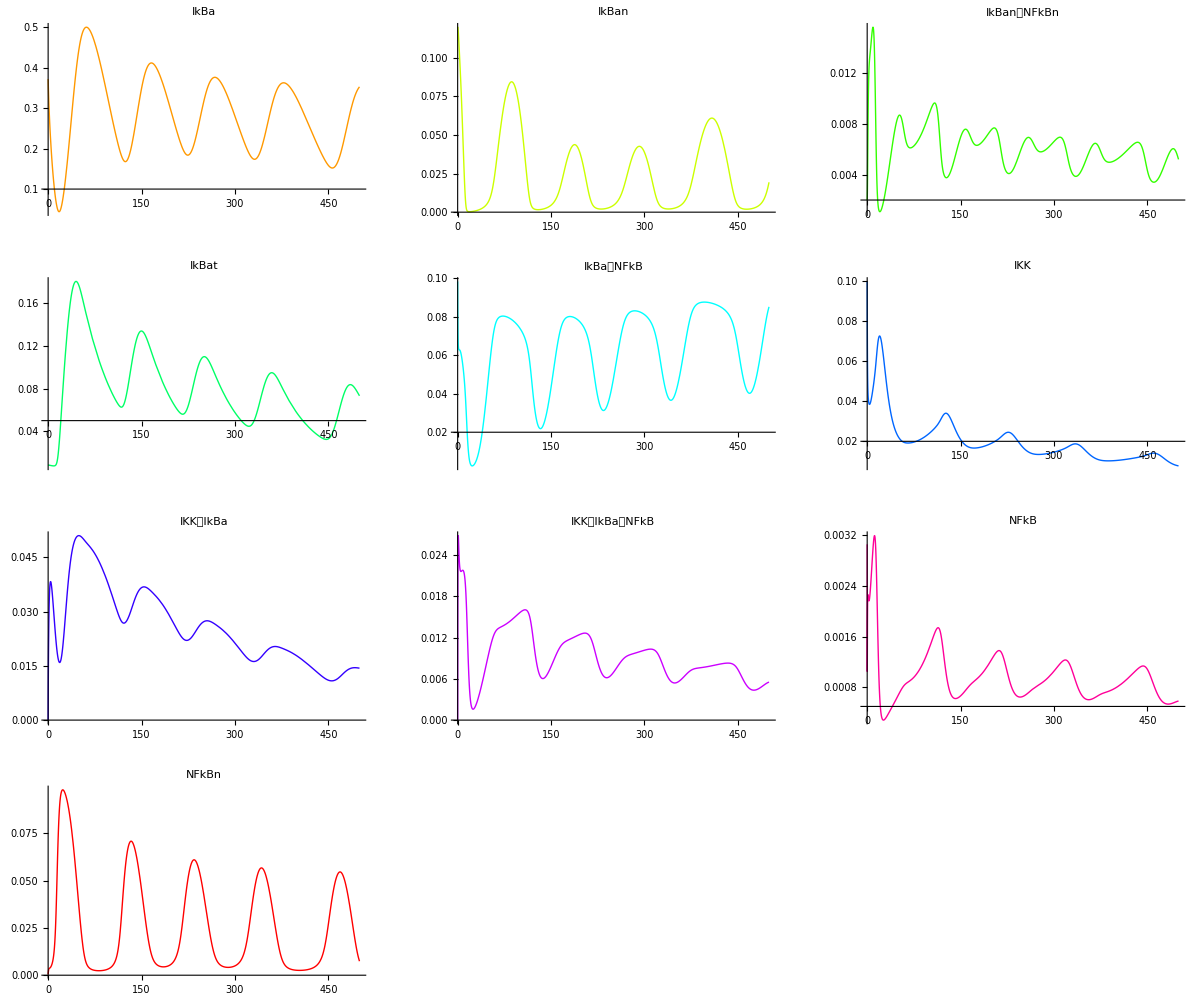

```mathematica
SBMLGridPlot[n,{IkBa,IkBan,IkBan⎵NFkBn,IkBat,IkBa⎵NFkB,IKK,IKK⎵IkBa,IKK⎵IkBa⎵NFkB,NFkB,NFkBn} ]
```

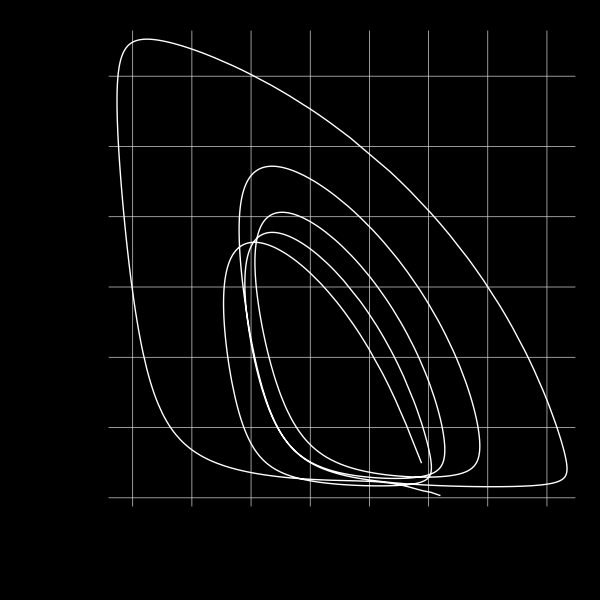

```mathematica
ParametricPlot[{NFKappaBeta`IkBa[t], NFKappaBeta`NFkBn[t]}/.Flatten[n], {t,0,500}, ImageSize-> 600,FrameLabel-> {"IkBa", "NFkBn"}, Frame-> True, TextStyle-> {LightBlue, FontFamily-> Times, FontSize-> 18},Background-> Black, PlotStyle-> White, AspectRatio-> 1, GridLines-> Automatic]
```